```mathematica
SetDirectory[NotebookDirectory[]];
Get["LearningNewtonsMethod/LearningNewtonsMethod.m"];
SetOptions[EvaluationNotebook[],Background->None]
SetOptions[SelectedNotebook[], 
         System`BackgroundAppearance -> ConvertImageToFullyScaledNinePatch[-Graphics-]];
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideZero"}]]
Grid[{{ GoBack[slidePrima, 0], GoHomepage[slidePrima], GoForward[slidePrima, 1]}}, ItemSize->Fit]
```

-Graphics- | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslidePrimaButtonDataHyperlinkHyperlinkActive

# -Graphics- | | | | Metodo di Newton | | | | | | | | | -Graphics- Anna Avena Matteo Sanfelici Giulia Cantini Roberto Ferraro Nicola Mainetti Matematica Computazionale Anno Accademico 2017/2018

## Legenda

In questo progetto alcune parole e concetti chiave saranno presentati sempre con gli stessi colori

Le funzioni saranno sempre blu
Gli zeri delle funzioni saranno sempre rossi
Le approssimazioni di questi saranno sempre verdi
La tolleranza dei metodi sarà sempre viola

Quando incontri questi colori saprai subito di cosa si sta parlando

## Prerequisiti

Prima di iniziare a studiare questo nuovo argomento assicurati di conoscere bene:

Cos’è una Funzione

Una funzione è una relazione tra due insiemi, chiamati dominio e codominio della funzione, che associa a ogni elemento del dominio uno e un solo elemento del codominio.

Cos’è una Equazione associata ad una funzione

L’equazione associata ad f(x) e` f(x)=0

Derivate in un punto

La derivata di una funzione in un punto z e` il limite del rapporto incrementale di quella funzione calcolata in z. Inoltre corrisponde al coefficente angolare della retta tangente al grafico della funzione nel punto di ascissa z

```mathematica
CellPrint[Cell["", "", CellTags -> {"slidePrima"}]]
Grid[{{ GoBack[slideZero, 1], GoHomepage[slidePrima], GoForward[slideSeconda, 1]}}, ItemSize->Fit]
```

-Graphics-8iype_shmslideZeroButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideSecondaButtonDataHyperlinkHyperlinkActive

## Outline

Presentazione del problema

Metodo di bisezione

Metodo delle secanti

Metodo di Newton

Funzionamento

Teoria

```mathematica
CellPrint[Cell["", "", CellTags->{"slideSeconda"}]]
Grid[{{ GoBack[slidePrima, 1], GoHomepage[slidePrima], GoForward[slideTerza, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslidePrimaButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideTerzaButtonDataHyperlinkHyperlinkActive

## Problema: ricerca di uno zero di una funzione

Ti sei mai chiesto come fa la calcolatrice a calcolare √2?

```mathematica
(* Button["Approfondimento 2", show] *)
```

Notiamo che (√2)^2-2=0,
quindi √2 è uno zero dellafunzione f(x)=x^2-2.

In altre parole,calcolare √2, è equivalente a definire f(x) e cercarne uno zero.

```mathematica
(* Button["Approfondimento 2", show] *)
```

In generale se voglio calcolare √α (con α>0), posso considerare f(x)=x^2-α.

La zero di f(x)  è √α.

```mathematica
(* Button["Approfondimento 3", show] *)
```

Ancora più in generale, se voglio calcolare α^(1/n)posso considerare f(x) = x^n-α.
La zero di f(x)  è α^(1/n).

La calcolatrice definisce f(x)=x^2-2 e cerca gli zeri di f(x).
La calcolatrice,inoltre,ci restituisce una rappresentazione decimale di √2

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideTerza"}]]
Grid[{{ GoBack[slideSeconda, 1], GoHomepage[slidePrima], GoForward[slideQuarta, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideSecondaButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideQuartaButtonDataHyperlinkHyperlinkActive

## Ma come si trova la rappresentazione decimale di uno zero di f(x)?

Questo problema potrebbe essere irrisolubile se il numero cercato fosse irrazionale poiché avrebbe infinite cifre decimali.

Ad esempio, √2 è un numero reale irrazionale, quindi con infinite cifre decimali dopo la virgola, e la calcolatice lo rappresenta come 1,4142...

Infatti è sempre possibile ottenere un’approssimazione anche con molte cifre decimali di un qualsiasi numero

## Teorema di Bolzano

```mathematica
Bolzano[]
```

Notiamo che la funzione f(x) = x^2-2 è continua

 e che f calcolata in a = 1 è negativa .

Inoltre notiamo che f calcolata in b = 2 è positiva .

Ciò che abbiamo appena osservato sono le ipotesi del Teorema di Bolzano.



Quindi possiamo esser certi che tra 1 e 2 è compreso un suo zero .

Teorema di Bolzano

Data una funzione f (x) continua in un intervallo [a, b] tale che f (a) f (b) < 0 allora 
∃ c ∈ [a, b] tale che f (c) =0.

ll ragionamento appena affrontato vale più in generale per qualunque funzione f(x) continua in un intervallo [a,b], che assume valori di segno opposto in a e b.

Vedremo ora 3 differenti metodi numerici per calcolare un valore approssimato di √2.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideQuinta"}]]
Grid[{{ GoBack[slideQuarta, 1], GoHomepage[slidePrima], GoForward[slideSesta, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideQuartaButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideSestaButtonDataHyperlinkHyperlinkActive

## Metodo di bisezione

Partendo dall’osservazione che f(x)=x^2-2 calcolata in 1 è negativa mentre calcolata in 2 è positiva, pensiamo di trovare un’approssimazione di √2 nel valore medio tra 1 e 2

(1+2)/2=1,5=x_1

GRAFICO di x^2-2 con 1 iterazione

```mathematica
BisectionInteractive[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSesta"}]]
Grid[{{ GoBack[slideQuinta, 1], GoHomepage[slidePrima], GoForward[slideSettima, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideQuintaButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideSettimaButtonDataHyperlinkHyperlinkActive

Verifichiamo ora che la funzione calcolata nell’approssimazione appena ottenuta x_1 assuma un valore vicino a 0;

f(1,5)=1,5^2-2=2,25-2=0,25

Poiché f calcolata in 1,5 è positiva mentre, come detto, calcolata in 1 è negativa possiamo dedurre che lo zero della funzione sia tra 1 e 1,5 ed assumerne come seconda approssimazione x_2 il valor medio tra 1 e 1,5

Ripetiamo il ragionamento (la parte sottolineata) dimezzando di volta in volta l’intervallo considerato ed otteniamo una successione di approssimazioni di √2 come mostrato in figura

Contuiniamo a cercare approssimazioni fin quando la differenza tra le ultime due trovate è minore di 0,0000001

GRAFICO di x^2-2 con molte iterazioni

Possiamo sfruttare lo stesso metodo che abbiamo usato per trovare un’approssimazione di √2per ricercare uno zero c di una qualsiasi funzione all’interno di un intervallo [a,b] purché f assuma in a ed in b valori di segno opposto. 

GIOCO di molte funzioni con molte iterazioni

Se abbiamo a che fare con numeri irrazionali potremmo non ottenere mai c ma sole sue approssimazioni.

In questo caso, o quando il numero ha troppe cifre decimali, decidiamo di essere soddisfatti quando l’ultima approssimazione x_i trovata non sia più grande o più piccola di c di un certo valore di tolleranza τ.

Poiché non conosciamo il valore di c  allora ci fermeremo quando la differenza tra x_i e x_(i-1) sara’ piu’ piccola di τ.

Formula

ALGORITMO DA METTERE IN UN RIQUADRO
Finché |a-b|> τ
c=(a+b)/2;
Se f(c)=0     BOTTONE abbiamo trovato il nostro zero
 STOP
Altrimenti
Se Segno(c)=Segno(a)
 a=c;           BOTTONE sappiamo che lo zero si trova tra c e b
Altimenti
 b=c;              BOTTONE sappiamo che lo zero si trova tra a e c 
Ritorna all’inizio

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSettima"}]]
Grid[{{ GoBack[slideSesta, 1], GoHomepage[slidePrima], GoForward[slideOttava, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideSestaButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideOttavaButtonDataHyperlinkHyperlinkActive

## Metodo delle secanti

Esistono altri metodi per calcolare √2?

Osservando il grafico qui sotto ci rendiamo subito conto che la retta secante f(x) nei punti (1;-1) e (2;2) interseca l’asse delle ascisse nel punto (0;1,OverBar[3]).

GRAFICO 1 secante UNA

1,OverBar[3] è un approssimazione di √2 migliore della prima che ci aveva restituito il metodo di bisezione, che era 1,5 ; 

Vediamo cosa succede reiterando il metodo:

GIOCO secanti su x^2-2 con iterazioni a scelta

Abbiamo quindi scoperto un’altra tecnica per la ricerca dell’approssimazione dello zero.

Sia P=(x_1,y_1) il punto di intersezione tra l’asse x e la retta che passa per i punti (a,f(a)) e (b,f(b)).
Assumiamo come valore approssimato dello zero il valore x_1,ovvero l’ascissa del punto P.

GRAFICO

Le coordinate di P sono le soluzioni del sistema

```mathematica
Piecewise[{{y=0, }, {(x-a)/(b-a) = (y - f(a))/(f(b) - f(a)), }}]
```

0

Si ottiene x_1 = a-(f(a)(b-a))/(f(b)-f(a))

```mathematica
(* TODO togliere colori e seguire la legenda iniziale *)
```

```mathematica
SecantAnimated[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideOttava"}]]
Grid[{{ GoBack[slideSettima, 1], GoHomepage[slidePrima], GoForward[slideNona, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideSettimaButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideNonaButtonDataHyperlinkHyperlinkActive

## Algoritmo

Finché |a-b|> τ
c= a-(f(a)*(b-a))/f(b)-f(a);
Se f(c)=0     BOTTONE abbiamo trovato il nostro zero
 STOP
Altrimenti
Se Segno(c)=Segno(a)
a=c;              BOTTONE sappiamo che lo zero si trova tra c e b
Altimenti
b=c;              BOTTONE sappiamo che lo zero si trova tra a e c
Ritorna all’inizio

# GIOCO secanti su molte funzioni con iterazioni a scelta

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideNona"}]]
Grid[{{ GoBack[slideOttava, 1], GoHomepage[slidePrima], GoForward[slideDecima, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideOttavaButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideDecimaButtonDataHyperlinkHyperlinkActive

### METODO DELLE TANGENTI

Il metodo della bisezione e quello delle secanti si sono rivelati 2 buoni metodi per approssimare √2 ma non sono i più “veloci”.

Isaac Newton (1642-1727) riuscì a trovare un metodo in grado di trovare approssimazioni dello zero di una funzione con la precisione voluta in molti meno passaggi.

IMMAGINE DI NEWTON GIF

L`idea di Newton è stata quella di considerare una approssimazione x_i del valore cercato e non  un intervallo come gli altri metodi.

Newton trova r retta tangente al grafico della funzione nel punto di ascissa x_i .

Calcola poi la successiva approssimazione x_(i+1) come l’ascissa del punto di intersezione tra la tangente r e l’asse delle x.

Osservando la finestra qui sotto è più facile capire il funzionamento del metodo:

GIOCO INTERATTIVO funzioni semplici

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideDecima"}]]
Grid[{{ GoBack[slideNona, 1], GoHomepage[slidePrima], GoForward[slideUndici, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideNonaButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideUndiciButtonDataHyperlinkHyperlinkActive

## Metodo di Newton (o delle tangenti) :

La retta r ha coefficiente angolare f ‘(x_i) e passa per il punto  (x_i,f(x_i)). 

Ha quindi equazione

y-f(x_i)=f’(x_i)*(x-x_i)

L’intersezione tra r e l’asse delle x è la soluzione del sistema:

```mathematica
Piecewise[{{y = 0, }, {y - f (a) = f '(a)(x-a), }}]
```

0

Si ottiene x_1 = a - (f(a))/(f'(a))

```mathematica
NewtonAnimated[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideUndici"}]]
Grid[{{ GoBack[slideDecima, 1], GoHomepage[slidePrima], GoForward[slideDodici, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideDecimaButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideDodiciButtonDataHyperlinkHyperlinkActive

### Algoritmo

## Finché |a-b|> τ c= a- (f(a)/f’(a)); a=b; b=c; Se f(b)=0 BOTTONE abbiamo trovato il nostro zero STOP Altrimenti Ritorna all’inizio GRAFICO confronto 3 metodi (sia soluzione che numero iterazioni)

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideDodici"}]]
Grid[{{ GoBack[slideUndici, 1], GoHomepage[slidePrima], GoForward[slideTredici, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideUndiciButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideTrediciButtonDataHyperlinkHyperlinkActive

## Teoria

Il metodo delle tangenti, o metodo di Newton, può presentare delle problematiche.

Nell’ esempio qui sotto si può notare che il metodo dà come seconda approssimazione dello zero un valore esterno al dominio della funzione.

Quindi non è possibile disegnare la seconda tangente per trovare una terza approssimazione.

```mathematica
FirstExample[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideTredici"}]]
Grid[{{ GoBack[slideDodici, 1], GoHomepage[slidePrima], GoForward[slideQuattordici, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideDodiciButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideQuattordiciButtonDataHyperlinkHyperlinkActive

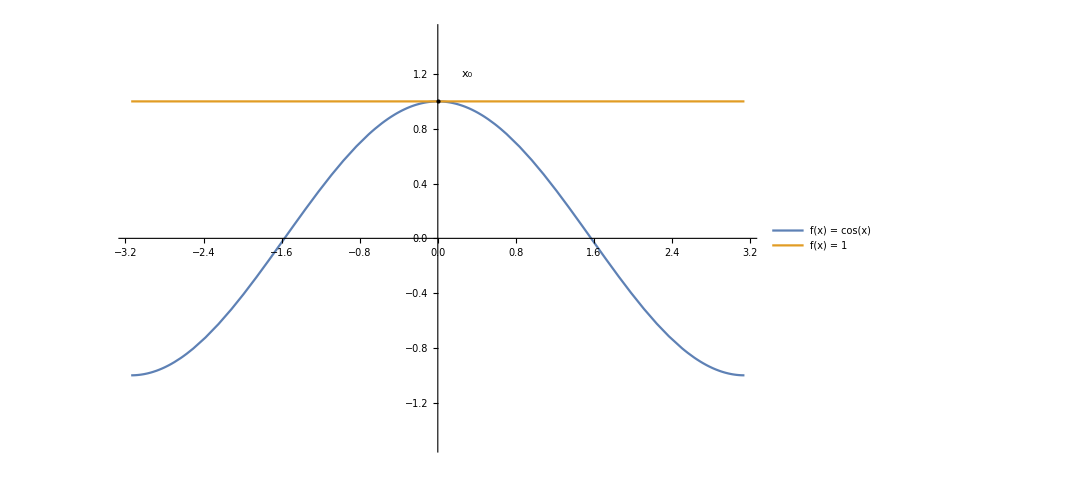

In quest’altro esempio invece possiamo notare che non è possibile calcolare neanche una prima approssimazione dello zero x_1 = a - (f(a))/(f'(a)) poiché  f ’ (a)=0.

Geometricamente si vede che la retta tangente al punto (0,1) è parallela all’asse delle x e quindi non lo incontra mai.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideQuattordici"}]]
Grid[{{ GoBack[slideTredici, 1], GoHomepage[slidePrima], GoForward[slideQuindici, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideTrediciButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideQuindiciButtonDataHyperlinkHyperlinkActive

Per ovviare a questi due possibili problemi possiamo limitarci ad usare questo metodo con opportune restrizioni:

Per prima cosa, come per tutti gli altri metodi, dobbiamo essere certi che esista uno zero, il che, per il teorema di bolzano, accade sempre se la funzione è continua ed assume valori sia positivi che negativi.

Inoltre chiediamo che il dominio della funzione sia tutto ℝ , per essere certi di non trovare mai approssimazioni dello zero che cadono fuori dal dominio.

Infine chiediamo che la funzione ammetta derivata prima e seconda (entrambe continue) e che la derivata prima, di volta in volta non si annulli nei punti assunti come approssimazione.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideQuindici"}]]
Grid[{{ GoBack[slideQuattordici, 1], GoHomepage[slidePrima], GoForward[slideSedici, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideQuattordiciButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideSediciButtonDataHyperlinkHyperlinkActive

Se sei curioso di sapere perché sotto queste restrizioni siamo certi che il metodo di Newton restituisce una soluzione vicina allo zero premi il bottone qui sotto!!!!!!

BOTTONE CHE APRE IL TEOREMA (QUELLO VECCHIO)

Teorema 1

Data la funzione f(x)

sia c un suo zero ed x_1 un suo valore approssimato; posto

				F(x)=x-(f(x)/f’(x))

e calcolata la successione

				x_i+1=F(x_i) con i=1,2…

se esiste un numero k<1 tale che nell’intervallo che contiene i punti x_1,x_2,…,c risulta

				|F’(x)|<=k

allora

				lim x_i=c per i→+infinito
Dimostrazione

Per prima cosa proviamo F(c)=c

				F(c)=c-(f(c)/f’(c))

ed essendo c una radice dell’equazione f(x)=0 segue f(c)=0 e quindi

				F(c)=c

Andiamo ora a calcolare la distanza tra x_2 e c

				x_2-c=F(x_1)-F(c)

Vogliamo applicare il teorema di Lagrange (o del valor medio) alla funzione F per ottenere

				x_2-c=(x_1-c)*F’(x)

con x appartenente all’intervallo (x_1,c)
Per fare ciò dobbiamo dimostrare che la funzione F(x) rispetti le ipotesi del teorema di Lagrange.
Per non appesantire la dimostrazione proveremo questo nel lemma successivo al teorema.

Usando l’ipotesi |F’(x)|<=k abbiamo

				|x_2-c|<=|x_1-c|*k

reiterando il ragionamento

				|x_(i+1)-c|<=|x_1-c|*(k^i)
ed essendo k<1 si ha

				lim |x_(i+1)-c|=0 per i→+(infinito)
e quindi

				lim x_i=c per i→+infinito

									c.v.d.

Lemma
La funzione F(x) del teorema precedente rispetta le ipotesi del teorema di Lagrange nell’intervallo che contiene i punti x_1,x_2,…,c

Dimostrazione
Ricordiamo che le ipotesi del teorema di Lagrange sono: la funzione continua e la funzione derivabile in tutto l’intervallo al piu’ escludendo gli estremi.

				F(x)=x-(f(x)/f’(x))

f(x) e’ stata supposta continua all’inizio di questo paragrafo.
Analogamente f’(x) e’ stata supposta continua e non nulla nei punti che ci interessano.
Quindi f(x)/f’(x) e’ una funzione continua e lo e’ anche la funzione F(x) in quanto somma di funzioni continue.
F’(x)=1-{[(f’(x))^2-f(x)*f’’(x)]/ (f’(x))^2}=1-1+[f(x)*f’’(x)/ f’(x))^2]= f(x)*f’’(x)/ f’(x))^2

F(x) e’ derivabile se f(x)*f’’(x)/ f’(x))^2 e’ continua nell’intervallo che ci interessa; essendo f(x) ed f’’(x) continue, come supposto ad inizio paragrafo, ed essendo f’(x)≠0 cio’ risulta vero.

											c.v.d.

Grazie a questo teorema e a questo lemma possiamo essere certi che per qualsiasi funzione, purche’ con le opportune restrizioni dette, ci e’ possibile trovare una approssimazione di un suo zero con  il metodo delle tangenti di Newton.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSedici"}]]
Grid[{{ GoBack[slideQuindici, 1], GoHomepage[slidePrima], GoForward[slideDiciassette, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideQuindiciButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideDiciassetteButtonDataHyperlinkHyperlinkActive

## Teorema 1

Data l' equazione f (x) = 0, sia z una radice ed x_1 un suo valore approssimato;

posto

F(x) = x - (f(x))/(f ' (x))

e calcolata la successione

x_i+ 1 = F(x_i) con i=1,2,...

se esiste un numero k < 1 tale che nell’intervallo che contiene i punti x_1,x_2,...,x_z risulta

|F'(x)|≤  k

allora

```mathematica
CellPrint@Cell[TextData[{Cell[BoxData[FormBox[StyleBox[RowBox[{UnderscriptBox["lim",RowBox[{"□","→","□"}]]," ","□"}],UnderscriptBoxOptions->{LimitsPositioning->False}],TraditionalForm]]]," "}],"Text"]
```

lim_(□→□) □

lim_(i→+∞) x_(1 = z)

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideDiciassette"}]]
Grid[{{ GoBack[slideSedici, 1], GoHomepage[slidePrima], GoForward[slideDiciotto, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideSediciButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideDiciottoButtonDataHyperlinkHyperlinkActive

## Dimostrazione

Per prima cosa proviamo F(z) = z

F(z) = z-(f(z))/(f ' (z))

ed essendo z una radice dell’equazione f(x) = 0 segue che f(z) = 0 e quindi

F(z) = z

Andiamo ora  a calcolare la distanza fra x_2 e z

x_2- z = F(x_1) - F(z)

Vogliamo applicare il teorema di Lagrange (o del valor medio) alla funzione F per ottenere

x_2- z = (x_1- z) * F'(x)

con x appartenente all’intervallo [ x_1, z ].

Per fare ciò dobbiamo dimostrare che la funzione F(x) rispetti le ipotesi del teorema di Lagrange.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideDiciotto"}]]
Grid[{{ GoBack[slideDiciassette, 1], GoHomepage[slidePrima], GoForward[slideDiciannove, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideDiciassetteButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideDiciannoveButtonDataHyperlinkHyperlinkActive

Per non appesantire la dimostrazione proveremo questo nel lemma successivo al teorema.

Usando l’ipotesi  |F'(x)|≤ k abbiamo

|x_2- z |≤ |x_1- z |* k

Iterando il ragionamento

|x_(i+1)- z |≤ |x_1- z |* (k^i)

Ed essendo k < 1 si ha

```mathematica
CellPrint@Cell[TextData[{Cell[BoxData[FormBox[StyleBox[RowBox[{UnderscriptBox["lim",RowBox[{"□","→","□"}]]," ","□"}],UnderscriptBoxOptions->{LimitsPositioning->False}],TraditionalForm]]]," "}],"Text"]
```

lim_(□→□) □

lim_(i→ +∞) |x_(i+1)-z|

e quindi

```mathematica
CellPrint@Cell[TextData[{Cell[BoxData[FormBox[StyleBox[RowBox[{UnderscriptBox["lim",RowBox[{"□","→","□"}]]," ","□"}],UnderscriptBoxOptions->{LimitsPositioning->False}],TraditionalForm]]]," "}],"Text"]
```

lim_(□→□) □

lim_(i→+∞)  x_i=z

c.v.d

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideDiciannove"}]]
Grid[{{ GoBack[slideDiciotto, 1], GoHomepage[slidePrima], GoForward[slideVenti, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideDiciottoButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideVentiButtonDataHyperlinkHyperlinkActive

## Lemma

La funzione F(x) del teorema precedente rispetta le ipotesi del teorema di Lagrange nell’intervallo che contiene i punti x_1,x_2,...,x_z.

## Dimostrazione

Ricordiamo che le ipotesi del teorema di Lagrange sono: la funzione continua e la funzione derivabile in tutto l’intervallo al più escludendo gli estremi.

F(x) = x-(f(x))/(f'(x))

f(x) è stata supposta all’inizio di questo paragrafo.

Analogamente f'(x) è stata supposta continua e non nulla nei punti che ci interessano.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideVenti"}]]
Grid[{{ GoBack[slideDiciannove, 1], GoHomepage[slidePrima], GoForward[slideVentuno, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideDiciannoveButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideVentunoButtonDataHyperlinkHyperlinkActive

Quindi (f(x))/(f'(x)) è una funzione continua e lo è anche la funzione F(x) in quanto somma di funzioni continue.

F'(x) =1-{(f'(x)^2-f(x)f'(x))/(f'(x)^2) }

= 1- 1+{ (f(x)f'(x))/(f'(x)^2) }

= { (f(x)f'(x))/(f'(x)^2)  }

F(x) è derivabile se (f(x)f'(x))/(f'(x)^2) è continua nell’intervallo che ci interessa; essendo f(x) ed f '(x) continue, come supposto ad inizio paragrafo, ed essendo f ‘(x) ≠ 0 ciò risulta vero.

c.v.d

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideVentuno"}]]
Grid[{{ GoBack[slideVenti, 1], GoHomepage[slidePrima], GoForward[slideVentidue, 1]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideVentiButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-8iype_shmslideVentidueButtonDataHyperlinkHyperlinkActive

Grazie a questo teorema e a questo lemma possiamo essere certi che per qualsiasi funzione, purché con le opportune restrizioni dette, ci è possibile trovare una approssimazione di un suo zero con il metodo delle tangenti di Newton.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideVentidue"}]]
Grid[{{ GoBack[slideVentuno, 1], GoHomepage[slidePrima], GoForward[slideVentitre, 0]}}, ItemSize -> Fit]
```

-Graphics-8iype_shmslideVentunoButtonDataHyperlinkHyperlinkActive | -Graphics-8iype_shmslidePrimaButtonData | -Graphics-